```mathematica
a=5;
```

```mathematica
b=3
```

3

```mathematica
a+b
```

8

```mathematica
a^b
```

125

```mathematica
Sqrt[(a+b)^3]
```

16 √2

```mathematica
TeXForm[√((a+b)^3)]
```

16 \sqrt{2}

```mathematica
TraditionalForm[Sqrt[(a+b)^3]]
```

16 √2

```mathematica
f=(√((x+y)^3))^30
```

(x+y)^45

```mathematica
Clear[a,b]
```

```mathematica
D[f,x]
```

45 (x+y)^44

```mathematica
f_[x,y;a,b]
```

```mathematica
a[t_]:=t^2
```

```mathematica
F[x_,y_]:=Sqrt[(x+y)^3]^30
```

```mathematica
D[F[x,y],x,y]
```

1980 (x+y)^43

```mathematica
Integrate[Sqrt[Tanh[x]],x]
```

-ArcTan[√Tanh[x]]-1/2 Log[-1+√Tanh[x]]+1/2 Log[1+√Tanh[x]]

```mathematica
Integrate[E^(-x^2),{x,-∞,∞}]
```

√π

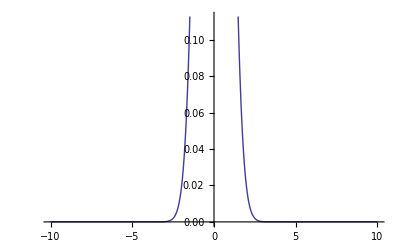

```mathematica
Plot[E^(-x^2),{x,-10,10}]
```

Solución de ecuaciones lineales y no lineales

```mathematica
Clear[a]
```

```mathematica
Solve[b-a==(a+b)^3,b]
```

{{b→-a-1/(3^(1/3) (9 a+√3 √(-1+27 a^2))^(1/3))-((9 a+√3 √(-1+27 a^2))^(1/3))/3^(2/3)},{b→-a+(1+ⅈ √3)/(2 3^(1/3) (9 a+√3 √(-1+27 a^2))^(1/3))+((1-ⅈ √3) (9 a+√3 √(-1+27 a^2))^(1/3))/(2 3^(2/3))},{b→-a+(1-ⅈ √3)/(2 3^(1/3) (9 a+√3 √(-1+27 a^2))^(1/3))+((1+ⅈ √3) (9 a+√3 √(-1+27 a^2))^(1/3))/(2 3^(2/3))}}

```mathematica
FullSimplify[-a-1/(3^(1/3) (9 a+√3 √(-1+27 a^2))^(1/3))-((9 a+√3 √(-1+27 a^2))^(1/3))/3^(2/3)]
```

-a-(3^(1/3)+(9 a+√(-3+81 a^2))^(2/3))/(3^(2/3) (9 a+√(-3+81 a^2))^(1/3))

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f.